# SIR model

## Setup Time, States, and Parameters

```mathematica
startYr=2007;
stopYr=2023;
timestep=1/12;
(*intv=2018-2007+timestep;*)
intv=1;

simYr=stopYr-startYr;
time=Range[0,simYr,timestep]//N ;(* Vector of years with 1/12 (ie months) stepsize*)

(*3 Logical vectors in Table format for intervention, access with intvT[[3]]*)
intvT =Table[If[#==intv+((X-1)*timestep),1,0]&/@time,{X,3}]; (*now obsolete*)
intvV=Boole[MemberQ[Table[intv+(timestep*x)//N,{x,0,2}],#]&/@time];
```

## Setup equation

NDSolve::ssres: NDSolve has computed values that give a zero residual for the differential-algebraic system, but some components are different from those specified.

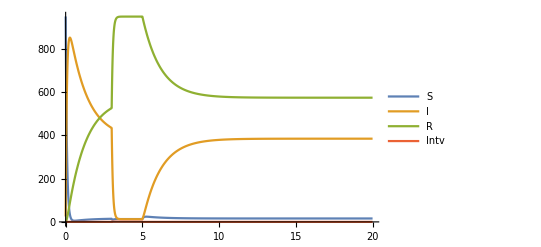

```mathematica
(*Boole[MemberQ[{1,2,3},dt[t]//N]]*)
(*On[NDSolve::overdet]*)
(*λ=0.05;
m=0.5;
ν=365/30;
ω=365/30;*)

Clear[λ,m,ν,ω];
eq={
dt[0]==0,
S[0]==950,
Inf[0]==25,
R[0]==0,
λ==0.335, (*0.005*)
m==0.5,
ν==365/30,
ω==365/30,
dt'[t]==1,(*timestep*)
(*If[dt[t]≥ 15,1,0]
intvS[t]==If[3≤ N[dt[t],9]<5,1,0],
If[3≤ dt[t]<5,1,0],
Piecewise[{{0,N[dt[t],10]≤  3},{1,3<N[dt[t],10]<5},{0,N[dt[t],10]≥ 5}}]
*)
intvS[t]==If[3≤ dt[t]<5,1,0],
S'[t]==ω R[t]-S[t] (λ+m*intvS[t]),
Inf'[t]==λ S[t]-Inf[t] (ν+m*intvS[t]),
R'[t]==(m*intvS[t]) S[t]+Inf[t] (ν+m*intvS[t])-ω R[t]
};
sol=NDSolve[eq,{dt,S,Inf,R, intvS},{t,0,20},  PrecisionGoal->12];
Plot[{S[t]/.sol, Inf[t]/.sol,R[t]/.sol, intvS[t]/.sol},{t,0,20}, PlotRange->All, PlotLegends->{"S","I","R","Intv"}]
```

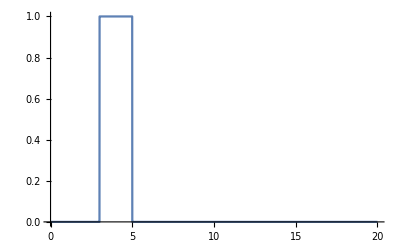

```mathematica
Plot[{intvS[t]/.sol},{t,0,20}, PlotRange->All]
```

```mathematica
If[x<4,a,b]/.x-> {1,3,5,6}
```

```mathematica
If[#<4,a,b]&/@ {1,3,5,6}
```

```mathematica
Length[Range[0,2,2/(12 2)]//N]
```

```mathematica
Range[0,2,2/(12 2)]//N
```

```mathematica
Boole[MemberQ[Table[intv+(timestep*x)//N,{x,0,2}],11.0+4/12]]
```

NDSolve::nderr: Error test failure at t == 2.; unable to continue.

{{dt→InterpolatingFunction[…],intvS→InterpolatingFunction[…]}}

-Graphics-

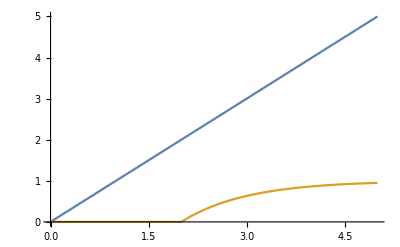

```mathematica
eqI={
dt[0]==0,
(*intvS[0]==0,*)
dt'[t]==1,
(*intvS'[t]==0,*)
intvS[t]==If[2.0≤ dt[t]<5.0,1,0]
}; (*Boole[MemberQ[{1,2,3},dt[t]]]*)
sol2 = NDSolve[eqI,{dt,intvS},{t,0,20}]
Plot[{dt[t]/.sol2, intvS[t]/.sol2},{t,0,20}, PlotRange->All]
```

```mathematica
MemberQ[Table[intv+(timestep*x)//N,{x,0,2}],0.5+timestep]
```

```mathematica
intv
```

```mathematica
If[#≥2,1,0]&/@time
```

testing out with delayed function

{{dt→InterpolatingFunction[…],S→InterpolatingFunction[…],Inf→InterpolatingFunction[…],R→InterpolatingFunction[…]}}

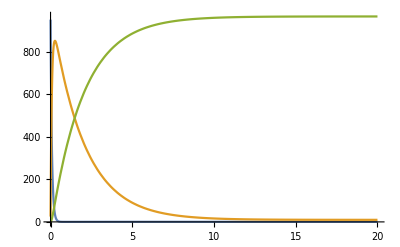

```mathematica
Clear[λ,m,ν,ω];
iPeriod[x_]:=If[x≥2,1,0]

eq={
dt[0]==0,
S[0]==950,
Inf[0]==25,
R[0]==0,
intvS[0]==0,
λ==0.005,
m==0.5,
ν==365/30,
ω==365/30,
dt'[t]==timestep,
(*If[dt[t]≥ 15,1,0]*)
intvS'[t]==iPeriod[dt[t]],
S'[t]==ω R[t]-S[t] (λ+m*intvS[t]),
Inf'[t]==λ S[t]-Inf[t] (ν+m*intvS[t]),
R'[t]==(m*intvS[t]) S[t]+Inf[t] (ν+m*intvS[t])-ω R[t]
};
sol=NDSolve[eq,{dt,S,Inf,R},{t,0,20}]
Plot[{S[t]/.sol, Inf[t]/.sol,R[t]/.sol},{t,0,20}, PlotRange->All]
```

```mathematica
iPeriod[x_]:=If[x≥2,1,0]
iPeriod[#]&/@time
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{{dt→InterpolatingFunction[…],S→InterpolatingFunction[…],Inf→InterpolatingFunction[…],R→InterpolatingFunction[…]}}

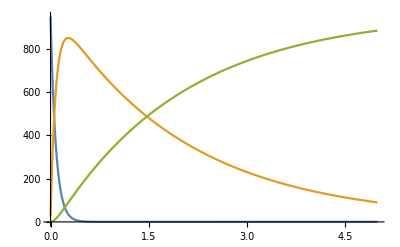

```mathematica
eq={
dt[0]==0,
S[0]==950,
Inf[0]==25,
R[0]==0,
λ==0.005,
m==0.5,
ν==365/30,
ω==365/30,
dt'[t]==timestep,
(*If[dt[t]≥ 15,1,0]*)
intvS[t] == iPeriod[dt[t]],
S'[t]==ω R[t]-S[t] (λ+m*intvS[t]),
Inf'[t]==λ S[t]-Inf[t] (ν+m*intvS[t]),
R'[t]==(m*intvS[t]) S[t]+Inf[t] (ν+m*intvS[t])-ω R[t]
};
sol=NDSolve[eq,{dt,S,Inf,R},{t,0,20}]
Plot[{S[t]/.sol, Inf[t]/.sol,R[t]/.sol},{t,0,5}, PlotRange->All]
```

```mathematica
If[2≤ #<5,1,0]&/@time
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
If[2≤ 3.2<5,1,0]
```

1